DateLong

# MSM + MS-TIS

## A MSM-based interface description for Multi-State Transition Interface Sampling

Jan-Hendrik Prinz

MSKCC, New York, US

jan.prinz@choderalab.org

David Swenson

Universiteit van Amsterdam (UvA), Amsterdam, The Netherlands

dwhs@hyperblazer.net

Weina Du

Universiteit van Amsterdam (UvA), Amsterdam, The Netherlands

w.du@uva.nl

Peter Bolhuis

Universiteit van Amsterdam (UvA), Amsterdam, The Netherlands

p.g.bolhuis@uva.nl

John D. Chodera

MSKCC, New York, US

john.chodera@choderalab.org

[ Abstract ]

## Section.INITIALIZATION

### Basic Packages

[ Here are the main packeges for every project ]

```mathematica
Module[{packagesToBeLoaded,result, $projectNameSelected,$basePath,$packagesPath},
$projectNameSelected=NotebookFileName[];
$basePath=FileNameTake[$projectNameSelected,{1,-2}];
$packagesPath = FileNameJoin[{$basePath,"packages"}];
SetDirectory[$packagesPath];
If[FileExistsQ[$packagesPath],
packagesToBeLoaded = Map[FileNameTake[#,-1]&,Select[FileNames["*",$packagesPath],FileType[#]==Directory&]];
result=Map[Needs[#<>"`"];&, packagesToBeLoaded];
CellPrint[Cell["Packages loaded : "<>StringJoin@Drop[Flatten@Map[{#,", "}&,Map[ToString,packagesToBeLoaded]],-1],"Text"]];
]
]
```

Packages loaded : MSM, NetCDFReader, PaperStyle, ProjectManagement

### InitializeProject

[ Create a project and put everything in a folder. If already done, just get the appropriate path variables ]

```mathematica
InitializeProject[];
```

### Additional Packages

[ Here go all additional packages to be loaded on startup ]

### Path settings

[ System specific paths and files set ]

### Options

[ All additional options to be set ]

### Functions

[ All necessary function initializations ]

## Section.INITIALIZATION

[ What's it about ]

### Davids Test U-Shape Potential

```mathematica
Module[{gauss,outer},
gauss[x_,y_,ax_,ay_,x0_,y0_]:=Exp[-ax*(x-x0)^2-ay*(y-y0)^2];
outer[x_,y_]:=x^6+y^6;
potential[x_,y_]:=outer[x,y]+6*gauss[x,y,30.0,1.5,0.0,0.6]+1.25*gauss[x,y,0.5,20.0,0.5,0.0]-0.5*y+0.75*gauss[x,y,1.0,5.0,0.5,-0.4]
]
```

```mathematica
potentialContourPlot=ContourPlot[f[x,y],{x,-1.25,1.25},{y,-1.25,1.30},PlotRange->{-0.5,4.0},ContourShading->None,Contours->20];
```

### Graphics Function

```mathematica
CutFunction::usage="Function specifying the shape to be plotted";
```

```mathematica
StripedShape[opts___]:=Module[{},
cutfn=CutFunction/.{opts};
mult=Direction/.{opts}/.{Direction->1};
Plot[Evaluate@Table[mult*x+n,{n,-2.5,2.5,0.025}],{x,-1.5,1.5},Evaluate@KeepOptions[Plot,opts],PlotPoints->40,AspectRatio->Automatic,Frame->None,PlotStyle->Directive[Black,Thin],PlotRange->{{-1.25,1.25},{-1.25,1.25}},RegionFunction->cutfn]
]
```

```mathematica
PositionContourPlot[p_,v_,opts___]:=Module[{},
ValueRange=ValueRange/.{opts}/.{ValueRange->Automatic};
Switch[ValueRange,
Automatic,
min=Min[v];
max=Max[v];
scale=0.5;
shift=0.5;,
Center,
min=0;
max=1;
scale=0.5;
shift=0.5;,
_,
min=0;
max=1;
scale=1;
shift=0;
];
val=Transpose@Join[Transpose[p],{shift+scale*(v-min)/(max-min)}];
ListContourPlot[val,KeepOptions[ListContourPlot,opts],MaxPlotPoints->1000]
]
```

### Interface Functions

Define an Interface “Class”

```mathematica
Interface/:MakeBoxes[Interface[l_?ListQ,opts:OptionsPattern[Interface]],StandardForm]:=InterpretationBox[#,Interface[l,opts]]&[RowBox[{SubscriptBox["𝕀",Dimensions[Centers[Interface[l,opts]]][[2]]],"[",Dimensions[Centers[Interface[l,opts]]][[1]],"/",Length@Inner[Interface[l,opts]],"]"}]]
Interface/:Interface[Interface[m_?ListQ,opts1:OptionsPattern[Interface]],opts2:OptionsPattern[Interface]]:=Interface[m,UnionRules[opts1,opts2]]
Interface/:NormalForm[Interface[m_?ListQ,opts:OptionsPattern[Interface]]]:={m,opts}
Interface/:Normal[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:=l
Interface/:Centers[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:="Centers"/.l
Interface/:Inner[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:="Inner"/.l
Interface/:NFn[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:="NearFunction"/.l
Interface/:Cutoff[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:="Cutoff"/.l
```

```mathematica
Interface/:Inside[Interface[l_?ListQ,opts:OptionsPattern[Interface]],p_]:=
Module[{},
m=Closest[Interface[l,opts],p];
in="Inner"/.l;
cf=Cutoff[Interface[l,opts]];
If[Length@Dimensions[m]==1,
m[[3]]<cf&&MemberQ[in,m[[1]]],
Map[#[[3]]<cf&&MemberQ[in,#[[1]]]&,m]
]
];
```

```mathematica
Interface/:Closest[Interface[l_?ListQ,opts:OptionsPattern[Interface]],p_]:=Module[{nfc,centers},
nfc="NearFunction"/.l;
centers="Centers"/.l;
If[Length@Dimensions[p]==1,
{#,centers[[#]],Norm[p-centers[[#]]]}&[nfc[p]//First],
Map[
{#,centers[[#]],Norm[p-centers[[#]]]}&[nfc[#]//First]&,
p]
]
];
```

```mathematica
Interface/:DrawIn[Interface[l_?ListQ,opts:OptionsPattern[Interface]],DIopts___]:=Module[{nfc,centers},
nfc="NearFunction"/.l;
centers="Centers"/.l;
fn=Function[{x,y},Module[{},
If[NumberQ[x],
Inside[Interface[l,opts],{x,y}],
False]
]];
RegionPlot[fn[x,y],{x,-1.55,1.55},{y,-1.55,1.55},Evaluate@KeepOptions[RegionPlot,DIopts]][[1]]
];
```

```mathematica
Interface/:DrawOut[Interface[l_?ListQ,opts:OptionsPattern[Interface]],DIopts___]:=Module[{nfc,centers},
nfc="NearFunction"/.l;
centers="Centers"/.l;
fn=Function[{x,y},Module[{},
If[NumberQ[x],
Inside[Interface[l,opts],{x,y}],
False]
]];
RegionPlot[!fn[x,y],{x,-1.55,1.55},{y,-1.55,1.55},Evaluate@KeepOptions[RegionPlot,DIopts]][[1]]
];
```

```mathematica
Interface/:SetInner[Interface[l_?ListQ,opts:OptionsPattern[Interface]],set_]:=Module[{},
newL=l;
ix=Idx[int[[1,All,1]],"Inner"]//First;
newL[[ix,2]]=set;
Interface[newL,opts]
]
```

```mathematica
Interface/:InFunc2[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:=Module[{},
Function[{x,y},Inside[Interface[l,opts],{x,y}]]
]
```

```mathematica
Interface/:InFunc3[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:=Module[{},
Function[{x,y,f},Inside[Interface[l,opts],{x,y}]]
]
```

```mathematica
Interface/:OutFunc2[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:=Module[{},
Function[{x,y},!Inside[Interface[l,opts],{x,y}]]
]
```

```mathematica
Interface/:OutFunc3[Interface[l_?ListQ,opts:OptionsPattern[Interface]]]:=Module[{},
Function[{x,y,f},!Inside[Interface[l,opts],{x,y}]]
]
```

```mathematica
Interface/:SelectIn[Interface[l_?ListQ,opts:OptionsPattern[Interface]],p_]:=Module[{},
Select[p,Inside[Interface[l,opts],#]&]
]
```

```mathematica
Interface/:SelectOut[Interface[l_?ListQ,opts:OptionsPattern[Interface]],p_]:=Module[{},
Select[p,(!Inside[Interface[l,opts],#])&]
]
```

### IO Functions

```mathematica
ReadXYZ[fn_,rows_:Span[2,All]]:=Module[{traj, frames},
traj=ReadList[fn,String];
frames=Map[StringSplit,traj[[3;;All;;3]]][[All,rows]];
Map[ToExpression,frames]
]
```

### Transition Matrix Functions

```mathematica
TransitionMatrix/:MeanFirstPassageTimeMatrix[TransitionMatrix[m_?MatrixQ,opts:OptionsPattern[TransitionMatrix]],optsMFPT:OptionsPattern[MeanFirstPassageTimeMatrix]]:=Module[{cM,nLagtime},
Table[MeanFirstPassageTime[tm,i],{i,Length[tm]}]
]
```

## Section.COMPUTATIONS

### Read Sample Trajectory in XYZ Format

```mathematica
frames=ReadXYZ[ToResourceFile["Upot.xyz"],{2,3}];
```

### Compute KMeans Voronoi Centers

KMeans is not very efficiently implemented. Takes a while, sorry!

```mathematica
kmean=KMeansClustering[frames,25];
```

```mathematica
centers=kmean;
nearfnc=Nearest[centers->Automatic];
discretized=Map[First[nearfnc[#]]&,frames];
cm=ToCountMatrix[TimeSeries[discretized]];
tm=MaximumLikelihoodMatrix[cm];
eq=Equilibrium@tm;
```

### Compute Random n-th Voronoi Centers

```mathematica
centers=frames[[1;;100000;;5000]];
nearfnc=Nearest[centers->Automatic];
discretized=Map[First[nearfnc[#]]&,frames];
cm=ToCountMatrix[TimeSeries[discretized]];
tm=MaximumLikelihoodMatrix[cm];
eq=Equilibrium@tm;
```

### Test Interface Class and Examples

```mathematica
int=Interface[{"Centers"->centers,"Inner"->Range[20],"NearFunction"->Nearest[centers->Automatic],"Cutoff"->0.1}]
```

𝕀_2[20/20]

```mathematica
SetInner[int,{1,2,3}]
```

𝕀_2[20/3]

```mathematica
Closest[int,{2,2}]
```

{9,{-0.444973,0.711821},2.76357}

```mathematica
Inside[int,{2,2}]
```

False

### Finc central cluster

```mathematica
mfptMatrix=MeanFirstPassageTimeMatrix[tm];
mfptAll=Map[Total,mfptMatrix];
```

```mathematica
centerID = Idx[eq,#==Max[eq]&]//First;
mfpt=MeanFirstPassageTime[tm,centerID];
```

Use average time reach a state when started from equilibrium (see script)

```mathematica
mfptMatrix=Table[MeanFirstPassageTime[tm,i],{i,Range[Length[tm]]}];
commuteAll=Map[Total,((mfptMatrix).DiagonalMatrix[eq])];
centerID = Idx[commuteAll,#==Min[commuteAll]&]//First;
mfpt=MeanFirstPassageTime[tm,centerID];
levelFunc[lev_]:=Module[{},
Idx[mfpt,#<lev&]
]
```

### Plotting

#### Plot Equilibrium

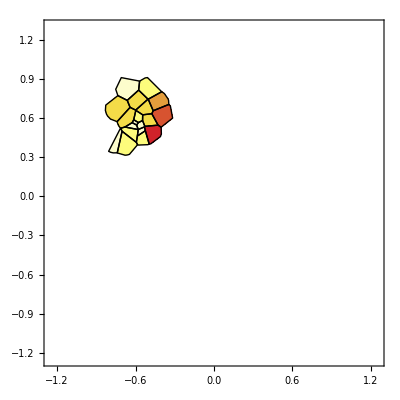

```mathematica
PositionContourPlot[centers,eq,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},RegionFunction->InFunc3[int],MaxPlotPoints->100,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]
```

#### Plot Centrality

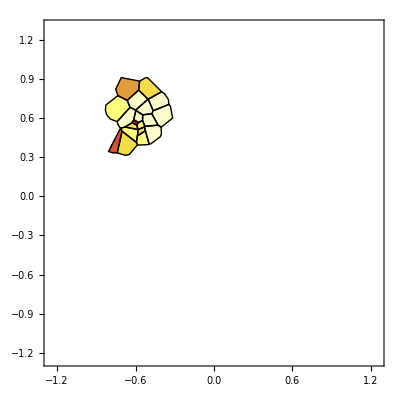

```mathematica
PositionContourPlot[centers,commuteAll,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},RegionFunction->InFunc3[int],MaxPlotPoints->20,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]
```

#### Other plot and fun stuff

```mathematica
Manipulate[
interfaceID=Idx[mfpt,#<level&];
Show[back,PositionContourPlot2[centers,mfpt,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},RegionFunction->inInterface[interfaceID],MaxPlotPoints->500,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]],
{level,0.001,Max[mfpt]+1}]
```

```mathematica
Manipulate[
Show[
PositionContourPlot[centers,mfpt,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},MaxPlotPoints->500,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],
Graphics[DrawOut[SetInner[int,levelFunc[level]],PlotRange->{{-1.25,1.25},{-1.25,1.30}},PlotPoints->40,ColorFunction->(White&)]],
ContourPlot[potential[x,y],{x,-1.25,1.25},{y,-1.25,1.30},PlotRange->{-0.5,4.0},PlotPoints->100,ContourShading->None,Contours->10,RegionFunction->(!InFunc3[SetInner[int,levelFunc[level]]][##]&)]
],
{level,0.001,Max[mfpt]+1}]
```

```mathematica
mov=Table[
Show[
PositionContourPlot[centers,mfpt,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},MaxPlotPoints->50,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],
Graphics[DrawOut[SetInner[int,levelFunc[level]],PlotPoints->80,BoundaryStyle->Directive[Dashed,Thick],PlotStyle->White,PlotRange->2*{{-1.25,1.25},{-1.25,1.30}}]],
potentialContourPlot,
Graphics[Text[Style["mfpt : "<>ToString[PaddedForm[level,{4,2}]],FontSize->32,FontFamily->"Gill Sans"],Scaled[{0.95,0.95}],{1,1}]]
,ImageSize->640,PlotRange->{{-1.25,0},{0,1.25}}],
{level,Sort[mfpt][[All]]}];
```

```mathematica
Export["/Users/jan-hendrikprinz/Desktop/test.mov",mov,"VideoEncoding"->"MPEG-4 Video",ImageSize->640]
```

```mathematica
pic[level_]:=Module[{},
interfaceID=Idx[mfpt,#<level&];
Show[
PositionContourPlot[centers,mfpt,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,1.25},{-1.25,1.30},{0,1}},MaxPlotPoints->50,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],
Graphics[DrawOut[SetInner[int,levelFunc[level]],PlotPoints->80,BoundaryStyle->Directive[Dashed,Thick],PlotStyle->White]],
potentialContourPlot,
Graphics[Text[Style["mfpt : "<>ToString[PaddedForm[level,{4,2}]],FontSize->32,FontFamily->"Gill Sans"],Scaled[{0.95,0.95}],{1,1}]]
,ImageSize->640,PlotRange->{{-1.25,0},{0,1.25}}]
];
```

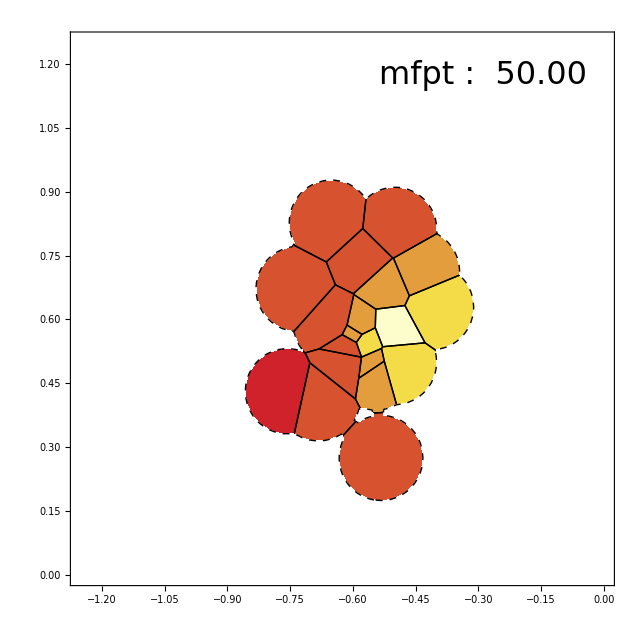

```mathematica
pic[50]
```

```mathematica
Show[{StripedShape[CutFunction->Function[{x,y},Inside[int,{x,y}]],Direction->1,PlotPoints->100,PlotStyle->Directive[Thickness[Medium],Black]],
StripedShape[CutFunction->Function[{x,y},Inside[int,{x,y}]],Direction->-1,PlotPoints->100,PlotStyle->Directive[Thickness[Medium],Black]]},PlotRange->{{-1.25,0},{0,1.25}}]
```

```mathematica
Show[{pic2[50,1],pic2[1,-1]}]
```

```mathematica
pic2[level_,dir_]:=Module[{},
Show[
Graphics[DrawIn[SetInner[int,levelFunc[level]],PlotPoints->100,BoundaryStyle->Directive[Dashed,Thick],PlotStyle->White]],StripedShape[CutFunction->Function[{x,y},Inside[SetInner[int,levelFunc[level]],{x,y}]],PlotPoints->200,PlotStyle->Directive[Thickness[Medium],Black],Direction->dir]
,ImageSize->640,PlotRange->{{-1.25,0},{0,1.25}}]
]
```

```mathematica
pic2[40]
```

```mathematica
lev=50;
Show[pic[lev],Graphics[{PointSize[0.001],Map[Point,SelectOut[SetInner[int,levelFunc[lev]],frames]]}],AspectRatio->Automatic]
```

```mathematica
centers2=KMeansClustering[SelectOut[SetInner[int,levelFunc[lev]],frames],25]
```

{{-0.382647,0.416406},{-0.838753,0.733418},{-0.839715,0.304616},{-0.387492,0.477537},{-0.423609,0.329344},{-0.879085,0.447596},{-0.838625,0.609074},{-0.650554,0.264613},{-0.846988,0.535249},{-0.361677,0.329559},{-0.584257,0.370633},{-0.41361,0.372689},{-0.344365,0.769242},{-0.540847,0.381146},{-0.419746,0.419269},{-0.764085,0.553481},{-0.77651,0.827081},{-0.40439,0.258451},{-0.356801,0.532464},{-0.425778,0.893829},{-0.493296,0.382901},{-0.45656,0.383884},{-0.341937,0.468017},{-0.337472,0.39481},{-0.745668,0.268342}}

#### Doesn’t work yet. Apparently for ListContourPlot one cannot set higher region function resolution. BUG?

```mathematica
int2=Interface[{"Centers"->centers2,"Inner"->Range[5],"NearFunction"->Nearest[centers2->Automatic],"Cutoff"->0.15}];
```

```mathematica
Module[{},
Show[{
PositionContourPlot[centers2,Range[25],InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,
PlotRange->{{-1.25,0},{0,1.30},{0,1}},MaxPlotPoints->200,ColorFunction->"TemperatureMap",ColorFunctionScaling->False],
Graphics[DrawOut[int2,PlotPoints->80,BoundaryStyle->Directive[Dotted,Thick],PlotStyle->White]],
PositionContourPlot[centers,mfpt,InterpolationOrder->0,BoundaryStyle->Black,ContourStyle->Black,PlotRange->{{-1.25,0},{0,1.30},{0,1}},MaxPlotPoints->100,ColorFunction->"TemperatureMap",ColorFunctionScaling->False,
RegionFunction->InFunc3[int],Mesh->Full],
Graphics[DrawIn[int,PlotPoints->80,BoundaryStyle->Directive[Dashed,Thick],PlotStyle->None]]
}]
]
```

## Section.RESULTS

[ Summary, Conclusions & Outlook ]

## Section.APPENDIX

[ Additional Material ]